# Taller de Matemática Tarea a Entregar

## Hinojosa Novales Hugo Alejandro No. De Cuenta: 31734152-6 Fecha: 20/03/2023 Ejercicio 1

a) Gráfica de la función

```mathematica
Clear[a,b]
g = (1/(a*(2*Pi)^(1/2)))*(Exp[(-1/2)*((x-b)/a)^2])
```

(ⅇ^(-(-b+x)^2/(2 a^2)))/(a √(2 π))

```mathematica
a = 1
b = 3
```

1

3

```mathematica
h = (1/(c*(2*Pi)^(1/2)))*(Exp[(-1/2)*((x-d)/c)^2])
```

(ⅇ^(-(-d+x)^2/(2 c^2)))/(c √(2 π))

```mathematica
c = 2
d = -3
```

2

-3

```mathematica
i = (1/(e*(2*Pi)^(1/2)))*(Exp[(-1/2)*((x-f)/e)^2])
```

(ⅇ^(-(-f+x)^2/(2 e^2)))/(e √(2 π))

```mathematica
e = -5
f = 3
```

-5

3

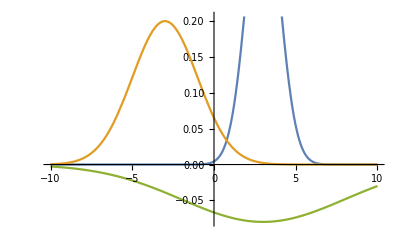

```mathematica
Plot[{g,h,i},{x,-10,10}]
```

b) Evaluación de la normalización

```mathematica
Integrate[g,{x,-Infinity,Infinity}]
Integrate[h,{x,-Infinity,Infinity}]
Integrate[i,{x,-Infinity,Infinity}]
```

1

1

-1

Se podría decir que todas cumplen con la normalización, pero utilizar
una constante negativa en la primera, provoca que salga negativa la integral

c) Ver si el cuadrado de la función cumple la normalización

```mathematica
Integrate[g^2,{x,-Infinity,Infinity}]
Integrate[h^2,{x,-Infinity,Infinity}]
Integrate[i^2,{x,-Infinity,Infinity}]
```

1/(2 √π)

1/(4 √π)

1/(10 √π)

Por ende no, no cumple la condición de normalización.

d) Resolver la ecuación pedida

```mathematica
Clear[a,b,c,d,e,f]
```

```mathematica
Solve[g == 1/2, x]
```

{{x→ConditionalExpression[b-√2 a √(2 ⅈ π C[1]+Log[(√(2/π))/a]), C[1]∈ℤ]},{x→ConditionalExpression[b+√2 a √(2 ⅈ π C[1]+Log[(√(2/π))/a]), C[1]∈ℤ]}}

## Ejercicio 2

a) Polinomio de grado 4 de Taylor alrededor del punto a = 6

```mathematica
f = x*Cos[x]+Log[x]
```

x Cos[x]+Log[x]

```mathematica
Clear[x]
```

```mathematica
Manipulate[((D[f,{x,n}])/(Factorial[n]))*(x-6)^n,{n,0,4,1}]
```

b) Construcción de función y gráfica

```mathematica
p =6Cos[6]+Log[6]+(-6+x)(1/6+Cos[6]-6Sin[6])+1/2 (-6+x)^2(-1/6^2-6 Cos[6]-2 Sin[6])+1/6 (-6+x)^3(2/6^3-3 Cos[6]+6 Sin[6])+1/24 (-6+x)^4(-6/6^4+6 Cos[6]+4 Sin[6])
```

6 Cos[6]+Log[6]+(-6+x) (1/6+Cos[6]-6 Sin[6])+1/2 (-6+x)^2 (-1/36-6 Cos[6]-2 Sin[6])+1/24 (-6+x)^4 (-1/216+6 Cos[6]+4 Sin[6])+1/6 (-6+x)^3 (1/108-3 Cos[6]+6 Sin[6])

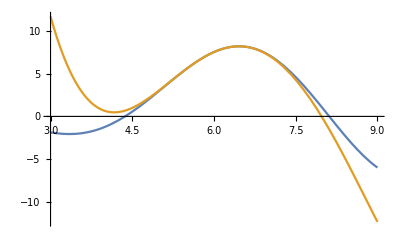

```mathematica
Plot[{f,p},{x,3,9}]
```

## Ejercicio 3

Definición de los tres tensores

```mathematica
A = {{3,7,3},{6,1,4},{3,3,1}}
```

{{3,7,3},{6,1,4},{3,3,1}}

```mathematica
MatrixForm[A]
```

(3 | 7 | 3
6 | 1 | 4
3 | 3 | 1)

```mathematica
B = {{2,8,1},{2,3,9},{1,4,2}}
MatrixForm[B]
M = {{1,1,7},{3,5,4},{2,3,1}}
MatrixForm[M]
```

{{2,8,1},{2,3,9},{1,4,2}}

(2 | 8 | 1
2 | 3 | 9
1 | 4 | 2)

{{1,1,7},{3,5,4},{2,3,1}}

(1 | 1 | 7
3 | 5 | 4
2 | 3 | 1)

a) (A^T)^{-1} = (A^{-1})^T

```mathematica
MatrixForm[Inverse[Transpose[A]]]
MatrixForm[Transpose[Inverse[A]]]
```

(-11/54 | 1/9 | 5/18
1/27 | -1/9 | 2/9
25/54 | 1/9 | -13/18)

(-11/54 | 1/9 | 5/18
1/27 | -1/9 | 2/9
25/54 | 1/9 | -13/18)

b) (AB)^{-1} = B^{-1}A^{-1}

```mathematica
MatrixForm[Inverse[A.B]]
MatrixForm[Inverse[B].Inverse[A]]
```

(-431/270 | -28/27 | 1171/270
277/810 | 20/81 | -767/810
41/162 | 11/81 | -103/162)

(-431/270 | -28/27 | 1171/270
277/810 | 20/81 | -767/810
41/162 | 11/81 | -103/162)

c) (ABC)^{-1} = C^{-1}B^{-1}A^{-1

```mathematica
MatrixForm[Inverse[A.B.M]]
MatrixForm[Inverse[M].Inverse[B].Inverse[A]]
```

(-4118/3645 | -647/729 | 11983/3645
6581/7290 | 493/729 | -18781/7290
-713/3645 | -86/729 | 1888/3645)

(-4118/3645 | -647/729 | 11983/3645
6581/7290 | 493/729 | -18781/7290
-713/3645 | -86/729 | 1888/3645)